```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
```

```mathematica
<<SetupEnvironment.m; (* Preferences like font sizes etc *)
<<EntrepreneurPFfunctions.m ;     (* loading functions *)
<<EntrepreneurPFparams.m ;            (* loading parameters *)
```

```mathematica
ShowVariableDefinitions
```

(𝒲 |  | entrepreneur's wage
α |  | Capital's Cobb-Douglas share
ψ |  | Firm's productivity
ℯ |  | Equity value of the firm
𝒻 |  | Firm's production function
𝒿 |  | Adjustment cost function
𝒾 |  | Investment
𝓀 |  | Firm's/Entrepreneur's physical capital
ι |  | Net investment ratio
ℜ |  | Riskless interest factor
𝒫 |  | After-ITC price of a unit of investment goods
τ |  | Corporate tax rate
ω |  | Adjustment cost parameter)

```mathematica
SolvePolFunc;(* solving the the unconstrained policy functions *)
```

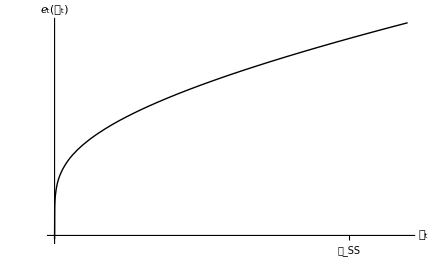

```mathematica
(* Value of the profit maximizing firm *)
MaxPlotRange=𝓀SS+𝓀SS/5;
Print[Plot[ℯSoln[𝓀Plot],{𝓀Plot,0,MaxPlotRange}
,AxesLabel->{"𝓀_t","ℯ_t(𝓀_t)"},Ticks->{{{𝓀SS,"𝓀_SS"}},None}
]];
```

### Policy functions plot over 𝓀_t holding 𝓂_t constant at 𝓂=1

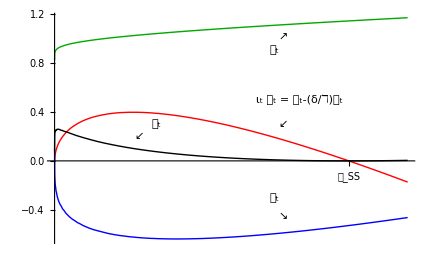

```mathematica
MaxPlotRange=𝓀SS+𝓀SS/5;
𝓂=1;
Print[PolFuncPlot=Show[Plot[{ιSoln[𝓀Plot]𝓀Plot,𝒸Func[𝓂,𝓀Plot],𝒿Soln[𝓀Plot],𝒶Soln[𝓂,𝓀Plot]}
,{𝓀Plot,0,MaxPlotRange}
,PlotStyle->{{Thick,Red},{Thick,Darker[Green]},{Thick,Black},{Thick,Blue}}
,AxesLabel->{"𝓀_t|_𝓂_t"},Ticks->{{{𝓀SS,"𝓀_SS"}},Automatic}],
Graphics[{
Text["𝒸_t",{2.6,.9}],Text[Style["↗",Large],{2.7,1.}],
Text["𝒶_t",{2.6,-.3}],Text[Style["↘",Large],{2.7,-.45}], (* Subscript[𝒶, t]=Subscript[𝓂, t]-Subscript[𝒸, t]-Subscript[𝒾, t]-Subscript[𝒿, t]*)
Text["ι_t 𝓀_t = 𝒾_t-(δ/ℸ)𝓀_t",{2.9,.5}],Text[Style["↙",Large],{2.7,.3}],
Text["𝒿_t",{1.2,.3}],Text[Style["↙",Large],{1,.2}]}]]];
```

## Phase Diagrams

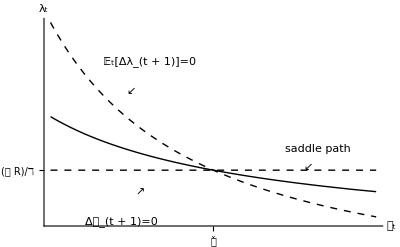

```mathematica
Print[lPhaseDiag=
Show[
    Plot[{λSaddle[𝓀Plot],Δ𝓀Equals0InλSpace[𝓀Plot],ΔλEquals0[𝓀Plot]},{𝓀Plot,𝓀SS 0.5,1.5𝓀SS}
    ,AxesOrigin->{𝓀SS 0.5,0.2},Ticks->{{{𝓀SS,"𝓀̌"}},{{𝒫 ℜ/ℸ,"(𝒫 R)/ℸ"}}}
    ,PlotStyle->{Black,{Dashed,Black},{Dashed,Black}},AxesLabel->{"𝓀_t","λ_t"},PlotRange->All],
Graphics[{
Text["𝔼_t[Δλ_(t + 1)]=0",{2.8,1.9}],Text[Style["↙",Large],{2.6,1.7}],
Text["saddle path",{4.6,1.3}],Text[Style["↙",Large],{4.5,1.18}],
Text["Δ𝓀_(t + 1)=0",{2.5,.8}],Text[Style["↗",Large],{2.7,1}]}]]];
```

```mathematica
Export["../../Figures/lPhaseDiag.pdf",lPhaseDiag];
Export["../../Figures/lPhaseDiag.eps",lPhaseDiag];
Export["../../Figures/lPhaseDiag.png",lPhaseDiag,ImageSize->72 9];
```

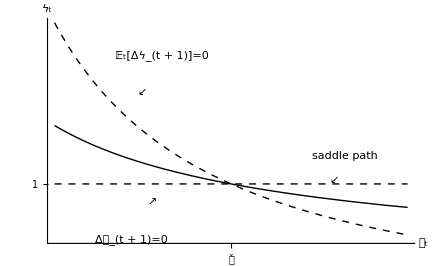

```mathematica
Print[qPhaseDiag=Show[
Plot[{ϟSaddle[𝓀Plot],Δ𝓀Equals0InϟSpace[𝓀Plot],Δϟ0[𝓀Plot]},{𝓀Plot,𝓀SS .5,1.5𝓀SS},AxesOrigin->{𝓀SS .5,0},Ticks->{{{𝓀SS,"𝓀̌"}},{{1,1}}},PlotStyle->{Black,{Dashed,Black},{Dashed,Black}},AxesLabel->{"𝓀_t","ϟ_t"}],
Graphics[{
Text["𝔼_t[Δϟ_(t + 1)]=0",{2.8,1.7}],Text[Style["↙",Large],{2.6,1.5}],
Text["saddle path",{4.6,1.15}],Text[Style["↙",Large],{4.5,1.02}],
Text["Δ𝓀_(t + 1)=0",{2.5,.7}],Text[Style["↗",Large],{2.7,.9}]}]]];
```

```mathematica
Export["../../Figures/qPhaseDiag.pdf",qPhaseDiag];
Export["../../Figures/qPhaseDiag.eps",qPhaseDiag];
Export["../../Figures/qPhaseDiag.png",qPhaseDiag,ImageSize->72 9];
```

## Impulse Response Functions

```mathematica
PreShockPeriods=5;
AfterShockPeriods=30;
```

```mathematica
Initialize:=Block[{},𝒶tm1=10;𝓀tList={𝓀SS};𝓂tList={(1-τ)(𝒲[𝓀SS]+𝒻'[𝓀SS])+𝒶tm1 ℜ};𝒸tList=𝒶tList=𝒾tList={};];
```

```mathematica
AddOnePeriod:=Block[{},
AppendTo[𝒸tList,𝒸Func[Last[𝓂tList],Last[𝓀tList]]];
AppendTo[𝒶tList,𝒶Soln[Last[𝓂tList],Last[𝓀tList]]];
AppendTo[𝒾tList,𝒾Soln[Last[𝓀tList]]];
AppendTo[𝓀tList,ℸ(Last[𝓀tList]+Last[𝒾tList])];
AppendTo[𝓂tList,(1-τ)(𝒲[Last[𝓀tList]]+Last[𝓀tList] 𝒻'[Last[𝓀tList]])+Last[𝒶tList] ℜ];
];
```

### Negative shock to 𝓂_t

Consider an entrepreneur with positive monetary resources owning a company at the steady state level of capital. Trace the dynamics of consumption, investment, invested capital and monetary resources if the latter are suddenly fully lost.

```mathematica
Initialize;
(* Simulation *)
Do[AddOnePeriod,{PreShockPeriods}];
𝓂tList[[-1]]=0; (* total loss of monetary resources *)
Do[AddOnePeriod,{AfterShockPeriods}];
```

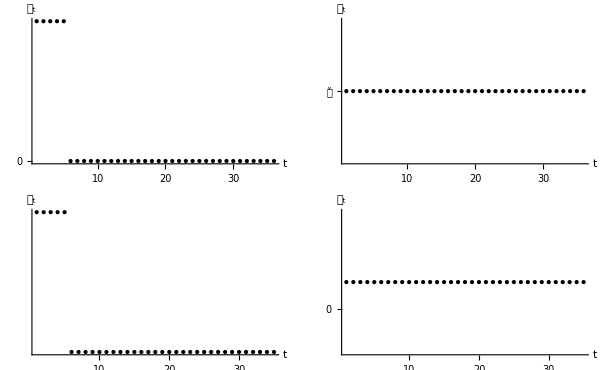

```mathematica
Print[mlossIRF=GraphicsGrid[{
{ListPlot[𝓂tList,AxesLabel->{"t","𝓂_t"},Ticks->{{},{0}},AxesOrigin->{0,0}],ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},Ticks->{{},{0,{𝓀SS,"𝓀̌"}}}]},
{ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},Ticks->{{},{0}},AxesOrigin->{0,0}],
ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},Ticks->{{},{0}},AxesOrigin->{0,0}]}
},ImageSize->600]];
```

```mathematica
Export["../../Figures/mlossIRF.pdf",mlossIRF];
Export["../../Figures/mlossIRF.eps",mlossIRF];
Export["../../Figures/mlossIRF.png",mlossIRF,ImageSize->72 9];
```

### Negative shock to 𝓀_t

Consider an entrepreneur with positive monetary resources owning a company at the steady state level of capital. Trace the dynamics of consumption, investment, invested capital and monetary resources if part of the invested capital is destroyed.

```mathematica
Initialize;
(* Simulation *)
Do[AddOnePeriod,{PreShockPeriods}];
𝓀tList[[-1]]=𝓀tList[[-1]]0.5; (* partial loss of capital *)
Do[AddOnePeriod,{AfterShockPeriods}];
```

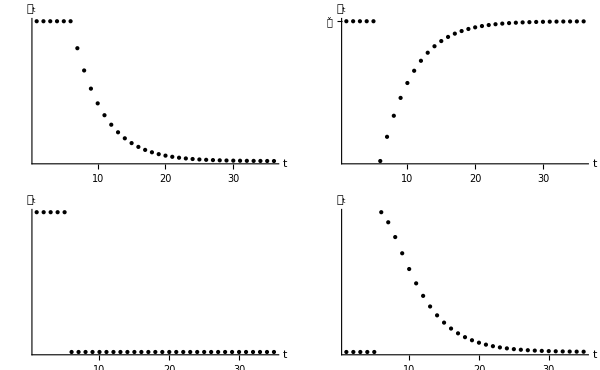

```mathematica
Print[klossIRF=GraphicsGrid[{
{ListPlot[𝓂tList,AxesLabel->{"t","𝓂_t"},Ticks->{{},{0}},AxesOrigin->{0,0}],ListPlot[𝓀tList,AxesLabel->{"t","𝓀_t"},Ticks->{{},{0,{𝓀SS,"𝓀̌"}}},AxesOrigin->{0,0}]},
{ListPlot[𝒸tList,AxesLabel->{"t","𝒸_t"},Ticks->{{},{0}},AxesOrigin->{0,0}],
ListPlot[𝒾tList,AxesLabel->{"t","𝒾_t"},Ticks->{{},{0}},AxesOrigin->{0,0}]}
},ImageSize->600]];
```

```mathematica
Export["../../Figures/klossIRF.pdf",klossIRF];
Export["../../Figures/klossIRF.eps",klossIRF];
Export["../../Figures/klossIRF.png",klossIRF,ImageSize->72 9];
```